## Initialisation

### fixed parameters

define ionisation potential, electric field amplitude  (intensity), fundamental wavelength...

```mathematica
ClearAll[Ip,ω,prefactor,r]
Ip=0.5;
ω = 0.057;
prefactor = ((ⅈ / Sqrt[π])*(2*Ip)^(1/4));
(*r={π/4,π/8,π/12}*)
(*r={π/4,π/6,π/8,π/10,π/12}*)
r={π/4,π/5,π/6,π/7,π/8,π/9,π/10,π/11,π/12,π/16,π/20,π/24,π/28,π/36,π/45,π/50,π/60,π/70,π/80,π/90,π/120,π/140,π/180,0}
```

{π/4,π/5,π/6,π/7,π/8,π/9,π/10,π/11,π/12,π/16,π/20,π/24,π/28,π/36,π/45,π/50,π/60,π/70,π/80,π/90,π/120,π/140,π/180,0}

### Define fields

electric  field  definition, vector potential, derivative of the action, action, ...

```mathematica
ClearAll[E1,Ax,Ay,A,Sf,Sfunc,DsFunc, D2sFunc,action]
(*Define the electric field function as a 2D vector*)
E1[t_,k_]:={Cos[k]*Cos[t],-Sin[k]*Cos[2t]};
(*Define the vector potential components*)
Ax[tx_,k_]:=-Integrate[E1[t,k][[1]],t]/. t->tx;
Ay[tx_,k_]:=-Integrate[E1[t,k][[2]],t]/. t->tx;
(*Define the 2D vector potential A*)
A[tx_,k_]:={Ax[tx,k],Ay[tx,k]};
Print[E1[t,k]]
Print[A[t,k]]

(*Define Sf,Sfunc,DsFunc,D2sFunc,and action in terms of px,Ax,py,and Ay*)
Sf[tk_,p_List,k_]=Integrate[2 (p[[1]]*Ax[t,k]+p[[2]]*Ay[t,k])+(Ax[t,k]^2+Ay[t,k]^2),t]/. t->tk;
Print[Sf[t,{px,py},k]]
Sfunc[t_,p_List,k_]:=0.5*Sf[t,p,k]+(0.5*(p[[1]]^2+p[[2]]^2)+Ip)*t;
Print[Sfunc[t,{px,py},k]]
DsFunc[t_,p_List,k_]:=D[Sfunc[tc,p,k],tc]/. tc->t;
Print[DsFunc[t,{px,py},k]]

D2sFunc[t_,p_List,k_]:=0.057*D[Sfunc[tz,p,k],{tz,2}]/. tz->t;
Print[D2sFunc[t,{px,py},k]]
D3sFunc[t_,p_List,k_]:=0.057*D[Sfunc[te,p,k],{te,3}]/. te->t;
Print[D3sFunc[t,{px,py},k]]
action[t_,p_List,k_]:=Exp[ⅈ*Sfunc[t,p,k]/0.057];
Print[action[t,{px,py},k]]
```

{Cos[k] Cos[t],-Cos[2 t] Sin[k]}

{-Cos[k] Sin[t],1/2 Sin[k] Sin[2 t]}

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

1/2 t Cos[k]^2+2 px Cos[k] Cos[t]-1/2 py Cos[2 t] Sin[k]+1/8 t Sin[k]^2-1/4 Cos[k]^2 Sin[2 t]-1/32 Sin[k]^2 Sin[4 t]

(0.5+0.5 (px^2+py^2)) t+0.5 (1/2 t Cos[k]^2+2 px Cos[k] Cos[t]-1/2 py Cos[2 t] Sin[k]+1/8 t Sin[k]^2-1/4 Cos[k]^2 Sin[2 t]-1/32 Sin[k]^2 Sin[4 t])

0.5+0.5 (px^2+py^2)+0.5 (Cos[k]^2/2-1/2 Cos[k]^2 Cos[2 t]+Sin[k]^2/8-1/8 Cos[4 t] Sin[k]^2-2 px Cos[k] Sin[t]+py Sin[k] Sin[2 t])

0.0285 (-2 px Cos[k] Cos[t]+2 py Cos[2 t] Sin[k]+Cos[k]^2 Sin[2 t]+1/2 Sin[k]^2 Sin[4 t])

0.0285 (2 Cos[k]^2 Cos[2 t]+2 Cos[4 t] Sin[k]^2+2 px Cos[k] Sin[t]-4 py Sin[k] Sin[2 t])

ⅇ^((0.+17.5439 ⅈ) ((0.5+0.5 (px^2+py^2)) t+0.5 (1/2 t Cos[k]^2+2 px Cos[k] Cos[t]-1/2 py Cos[2 t] Sin[k]+1/8 t Sin[k]^2-1/4 Cos[k]^2 Sin[2 t]-1/32 Sin[k]^2 Sin[4 t])))

```mathematica
DsFunc[t,{px,py}, θ]//Simplify
```

0.5+0.5 px^2+0.5 py^2+(0.25-0.25 Cos[2 t]) Cos[θ]^2-1. px Cos[θ] Sin[t]+1. py Cos[t] Sin[t] Sin[θ]+0.0625 Sin[θ]^2-0.0625 Cos[4 t] Sin[θ]^2

```mathematica
D2sFunc[t,{px,py},θ]//Simplify
```

-0.057 px Cos[t] Cos[θ]+0.057 Cos[t] Cos[θ]^2 Sin[t]+Sin[θ] (0.057 py Cos[2 t]+0.01425 Sin[4 t] Sin[θ])

### Define the momentum grid

```mathematica
ClearAll[pxValues,pyValues]
(*Define the range for px and py values*)
pxValues=Range[-3,3,0.1];
pyValues=Range[-3,3,0.1];
Print[Length[pxValues]]
Print[Length[pyValues]]
```

61

61

### Define plotting functions

```mathematica
ClearAll[plotEx,plotEy,plotRoots](*Plot Ex and Ey and roots*)
plotEx:=Quiet[Plot[E1[t][[1]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotEy:=Quiet[Plot[E1[t][[2]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ey"},ImageSize->Large]];

plotRoots[filteredTValues_]:=Quiet[ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

### Create Grid of Seeds

```mathematica
ClearAll[realMax,realMin,imagMax,imagMin,realSteps,imagSteps,listofseeds,initialGuess,listofseeds,seedPoints]
(*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMin=-2.133;realMax=4.150;
imagMin=0;imagMax=5;
realSteps=10;imagSteps=10;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];

(*Add the specific initial guess to the list of seeds*)
initialGuess=-2.0334+1.2321 ⅈ;
listofseeds=Prepend[listofseeds,initialGuess]

(*Ensure seeds are numerical values*)
listofseeds=N[listofseeds];

(*Extract real and imaginary parts of the seeds*)
seedPoints={Re[#],Im[#]}&/@listofseeds;
```

{-2.0334+1.2321 ⅈ,-2.133,-2.133+0.5 ⅈ,-2.133+1. ⅈ,-2.133+1.5 ⅈ,-2.133+2. ⅈ,-2.133+2.5 ⅈ,-2.133+3. ⅈ,-2.133+3.5 ⅈ,-2.133+4. ⅈ,-2.133+4.5 ⅈ,-2.133+5. ⅈ,-1.5047,-1.5047+0.5 ⅈ,-1.5047+1. ⅈ,-1.5047+1.5 ⅈ,-1.5047+2. ⅈ,-1.5047+2.5 ⅈ,-1.5047+3. ⅈ,-1.5047+3.5 ⅈ,-1.5047+4. ⅈ,-1.5047+4.5 ⅈ,-1.5047+5. ⅈ,-0.8764,-0.8764+0.5 ⅈ,-0.8764+1. ⅈ,-0.8764+1.5 ⅈ,-0.8764+2. ⅈ,-0.8764+2.5 ⅈ,-0.8764+3. ⅈ,-0.8764+3.5 ⅈ,-0.8764+4. ⅈ,-0.8764+4.5 ⅈ,-0.8764+5. ⅈ,-0.2481,-0.2481+0.5 ⅈ,-0.2481+1. ⅈ,-0.2481+1.5 ⅈ,-0.2481+2. ⅈ,-0.2481+2.5 ⅈ,-0.2481+3. ⅈ,-0.2481+3.5 ⅈ,-0.2481+4. ⅈ,-0.2481+4.5 ⅈ,-0.2481+5. ⅈ,0.3802,0.3802+0.5 ⅈ,0.3802+1. ⅈ,0.3802+1.5 ⅈ,0.3802+2. ⅈ,0.3802+2.5 ⅈ,0.3802+3. ⅈ,0.3802+3.5 ⅈ,0.3802+4. ⅈ,0.3802+4.5 ⅈ,0.3802+5. ⅈ,1.0085,1.0085+0.5 ⅈ,1.0085+1. ⅈ,1.0085+1.5 ⅈ,1.0085+2. ⅈ,1.0085+2.5 ⅈ,1.0085+3. ⅈ,1.0085+3.5 ⅈ,1.0085+4. ⅈ,1.0085+4.5 ⅈ,1.0085+5. ⅈ,1.6368,1.6368+0.5 ⅈ,1.6368+1. ⅈ,1.6368+1.5 ⅈ,1.6368+2. ⅈ,1.6368+2.5 ⅈ,1.6368+3. ⅈ,1.6368+3.5 ⅈ,1.6368+4. ⅈ,1.6368+4.5 ⅈ,1.6368+5. ⅈ,2.2651,2.2651+0.5 ⅈ,2.2651+1. ⅈ,2.2651+1.5 ⅈ,2.2651+2. ⅈ,2.2651+2.5 ⅈ,2.2651+3. ⅈ,2.2651+3.5 ⅈ,2.2651+4. ⅈ,2.2651+4.5 ⅈ,2.2651+5. ⅈ,2.8934,2.8934+0.5 ⅈ,2.8934+1. ⅈ,2.8934+1.5 ⅈ,2.8934+2. ⅈ,2.8934+2.5 ⅈ,2.8934+3. ⅈ,2.8934+3.5 ⅈ,2.8934+4. ⅈ,2.8934+4.5 ⅈ,2.8934+5. ⅈ,3.5217,3.5217+0.5 ⅈ,3.5217+1. ⅈ,3.5217+1.5 ⅈ,3.5217+2. ⅈ,3.5217+2.5 ⅈ,3.5217+3. ⅈ,3.5217+3.5 ⅈ,3.5217+4. ⅈ,3.5217+4.5 ⅈ,3.5217+5. ⅈ,4.15,4.15+0.5 ⅈ,4.15+1. ⅈ,4.15+1.5 ⅈ,4.15+2. ⅈ,4.15+2.5 ⅈ,4.15+3. ⅈ,4.15+3.5 ⅈ,4.15+4. ⅈ,4.15+4.5 ⅈ,4.15+5. ⅈ}

Find  all  the  roots for all px and py values (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for given px and py*)
generatePlotAndRoots[px_,py_,seeds_,k_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},
(*Find roots*)
allSolutions=Round[t/. Quiet[Table[FindRoot[DsFunc[t,{px,py},k]==0,{t,tseed}],{tseed,seeds}]],0.0001];
complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];
(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,{px,py},k]]]<=tolerance&&Abs[Im[DsFunc[#,{px,py},k]]]<=tolerance&];
{filteredTValues}];
```

# CALCULATION : Saddle Point Solutions

## ignore this kernel if results is already stored in the kernel! only run kernel below this one which says ' run this'

```mathematica
ClearAll[k]

DateString[]
(*Generate results using the precise px and py values*)
results23=
(*ParallelTable works similarly to Table,but it distributes the computation across multiple CPU cores,allowing for parallel execution and significantly speeding up the process.*)
Table[ParallelTable[
generatePlotAndRoots[px,py,listofseeds,r[[i]]],
{px,pxValues}, {py,pyValues}
],{i,Length[r]}]
DateString[]
```

Wed 5 Mar 2025 14:05:59

Wed 5 Mar 2025 14:13:35

#### this cell saves the array of data to the kernel

```mathematica
ClearAll[SaveToCell]
SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occurrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
SaveToCell[results23,"results23"]
```

## RUN THIS CELL results23= ‘results23’ below!

```mathematica
results23="results23";
```

### This restructures the data, to allow for plots below, MUST RUN AFTER RESULTS ARE GENERATED

```mathematica
ClearAll[newResults,pxValue,pyValue,tsExtended,validData]
(*this now iterates over all different mixing angles as the calculations goes for one mixing angle all combinations of px and py will produce {{{px,py,{ts1,ts2,ts3,ts4}},different{px,py,{ts1,ts2,ts3,ts4}}, and so on} thats for the first r, now for the next mixing angle r[...}, and so on}. so hopefully this explains my iteration choices.*)
newResults=
Table[Table[{
(*Calculate pxValue based on the index i*)
pxValue=-3+(i-1)*0.1,
(*Calculate pyValue based on the index j*)
pyValue=-3+(j-1)*0.1,
(*Extract the corresponding results for the current px and py values*)
results23[[q,i,j]]},
(*Iterate over the length of the results list for both i and j*)
{i,Length[results23[[q]]]},{j,Length[results23[[q]]]}
],{q,Length[r]}];

(*Flatten the newResults list by one level to get a list of sublists, Map over each sublist in flattenedResults For each sublist elem,join the first two elements with the elements of the nested list inside the third element.*)
tsExtended=Table[Map[Function[{elem},Join[{elem[[1]],elem[[2]]},elem[[3,1]]]],Flatten[newResults[[i]],1]],{i,Length[r]}];
(*so essentially grabbing px and py and putting them in the same array as the time saddle point solutions ts1,ts2,ts3,ts4 so the array of arrays will look like {{px,py,ts1,ts2,ts3,ts4},repeat for different values of px and py}*)


(*-validData is a list of lists of lists where each sublist contains four elements {Real part of ts,Imaginary part of ts,px,py}.*)
validData=
(*iterates over all mixing angles r so then it starts looking at the first r, which a list of list as described earlier in new results. and so on for all r values*)
Table[
(*Select elements from the list that satisfy a condition*)
Select[
(*Flatten the nested list into a list of lists*)
Flatten[
(*Generate a table of values*)
Table[
(*Conditional statement to check if the element is not Null*)
If[tsExtended[[q,i,j+2]]=!=Null,
{(*Real part of the complex number*)
Re[tsExtended[[q,i,j+2]]],
(*Imaginary part of the complex number*)
Im[tsExtended[[q,i,j+2]]],
(*px value*)
tsExtended[[q,i,1]],
(*py value*)
tsExtended[[q,i,2]]},
(*If the element is Null,return Nothing*)
Nothing],
(*Iterate over all rows of tsExtended*)
{i,Length[tsExtended[[q]]]},
(*Iterate over all columns except the first two, px and py.*)
{j,1,Length[tsExtended[[q,i]]]-2}],
(*-Flatten at level 1 converts the nested list into a list of lists*)
1],
(*-Select filters the flattened list to include only the elements where the first element is not Null*)
#[[1]]=!=Null&],
(*iterates over all mixing angles r*)
{q,Length[r]}]

(*(*length of valid data should be equal to the check solutions variable, if not there are missing saddle points as every saddle point px and py should have 4 saddle points*)
checksolutions1 = Length[pxValues]*Length[pyValues]*4*Length[r];
checksolutions2=Total[Table[Length[validData[[i]]], {i,Length[r]}]];
MissingSaddles=checksolutions1-checksolutions2;
Print["\n I should have ",checksolutions1,", Saddle points, but I have calculated/found ",checksolutions2,", So I have ",MissingSaddles," Missing Saddle Points."]
*)

(*Extract real and imaginary times from validData*)
realAndImagTimes=Table[validData[[q,All,1;;2]],{q,Length[r]}];
(*First need to iterate over all the mixing angles r, then [[All,1;;2]] is a part specification that extracts specific elements from each sublist. All indicates that we want to apply the extraction to all sublists in validData.   
1;;2 specifies the range of elements to extract from each sublist. In this case it extracts the first and second element [the real and imaginary parts of the saddle point solutions]*)
```

#### plotting the saddle points found in results

```mathematica
(*(*Extract real and imaginary parts*)
extraction=
Table[
Map[
{Re[#],Im[#]}&,
Flatten[results23[[i]]]
],
{i,Length[r]}];

(*Plot the time saddle points*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],
ListPlot[
{extraction[[i]]},
AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Complex Time Plane: Saddle Points",ImageSize->Large]}],
{{i,1,"Index"},1,Length[r],1}*)
]
```

Part::partd: Part specification extraction⟦1⟧ is longer than depth of object.

# (3D) Complex Plane Saddle Points Indexed Momentum via Colour (3D)

```mathematica
(*Plot the time saddle points*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],
ListPlot[
{realAndImagTimes[[i]]},
AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Complex Time Plane: Saddle Points",ImageSize->Large]}],
{{i,1,"Index"},1,Length[r],1}
]
```

Part::partd: Part specification realAndImagTimes[[1]]
     is longer than depth of object.

General::prng: Value of option PlotRange -> 
    {{realMin, realMax}, {imagMin, imagMax}}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

Part::partd: Part specification realAndImagTimes[[1]]
     is longer than depth of object.

General::prng: Value of option PlotRange -> 
    {{realMin, realMax}, {imagMin, imagMax}}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

Part::partd: Part specification realAndImagTimes[[1]]
     is longer than depth of object.

General::prng: Value of option PlotRange -> 
    {{realMin, realMax}, {imagMin, imagMax}}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

```mathematica
|
```

```mathematica
(*Plot the 3D graph with color representing px*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],

ListPointPlot3D[{#[[1]],#[[2]],#[[3]]}&/@validData[[i]],ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"3D Data Representation",ImageSize->Large, PlotRange->{{realMin,realMax},{imagMin,imagMax}},(*ViewPoint->{5,-5,5}, ViewVertical->{0,0,1}*)ViewPoint->{0,0,10}, ViewVertical->{0,0,1} 
(*,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Bottom}]*)]
}],
{{i,1,"Index"},1,Length[r],1}
]
(*comment i want to extract the indexed momentums px and py, for corresponding r mixing angle and the time saddle points arrays, to have one time array like realandimagtimes, and to have a momentum array which is correctly indexed according to realandimagtimes to look like {{{px1,py1},{px2,py2},{px3,py3}, and so on...},for different r{{px1,py1},{px2,py2},{px3,py3}, and so on...} for all values of r...}. and then essentially just plot the two correspondingly, would that make it less computationally taxing to plot then just iterating through valid data and plotting the values? *)
```

Part::partd: Part specification validData[[1]] is longer than depth of object.

Part::partd: Part specification validData[[2]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::pkspec1: The expression {1[[1]], 1[[2]], 1[[3]]}
     cannot be used as a part specification.

Automatic::prng: 
   Value of option PlotRange -> {{realMin, realMax}, {imagMin, imagMax}}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

ListPointPlot3D::ldata: 
   {validData[[1]], validData[[2]], validData[[3]]}[[{1[[1]], 1[[2]], 
      1[[3]]}]] is not a valid dataset or list of datasets.

```mathematica
(*Plot the 3D graph with color representing py*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],

ListPointPlot3D[{#[[1]],#[[2]],#[[4]]}&/@validData[[i]],ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","py"},PlotLabel->"3D Data Representation",ImageSize->Large, PlotRange->{{realMin,realMax},{imagMin,imagMax}},(*ViewPoint->{5,-5,5}, ViewVertical->{0,0,1}*)ViewPoint->{0,0,10}, ViewVertical->{0,0,1} 
(*,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Bottom}]*)]
}],
{{i,1,"Index"},1,Length[r],1}
]
(*comment i want to extract the indexed momentums px and py, for corresponding r mixing angle and the time saddle points arrays, to have one time array like realandimagtimes, and to have a momentum array which is correctly indexed according to realandimagtimes to look like {{{px1,py1},{px2,py2},{px3,py3}, and so on...},for different r{{px1,py1},{px2,py2},{px3,py3}, and so on...} for all values of r...}. and then essentially just plot the two correspondingly, would that make it less computationally taxing to plot then just iterating through valid data and plotting the values? *)
```

# Finding Fold & Cusp Points & 2D plots to check!

```mathematica
r[[14]]
r[[10]]
```

π/36

π/16

### Generate grid of seeds

```mathematica
ClearAll[realMaxi,realMini,imagMaxi,imagMini,realSteps,imagSteps,listofseeds1]
(*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMini=-2.5;realMaxi=2.5; (*pick ranges based off plots*)
imagMini=1.5;imagMaxi=3;  
realSteps=10;imagSteps=10;

listofseeds1=Flatten[Table[x+I y,{x,realMini,realMaxi,(realMaxi-realMini)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];
```

### Find fold points iterating through grid of seeds

```mathematica
foldpoints=Quiet[Block[{k=5,tguess, pxguess, pyguess,Retguess,Imtguess},
Retguess=-2.0334;
Imtguess=1.2321;
pyguess=0;
pxguess=(*3*)3;
Table[Block[{Ret,Imt},
Retguess = Re[t];Imtguess=Im[t];
FindRoot[
{Re[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Re[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Im[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Im[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0
},{Ret,Retguess},{Imt,Imtguess},{px, pxguess},{py,pyguess}]]
,{t,listofseeds1}]
]];
```

```mathematica
θRange
```

```mathematica
thing=Block[{k=10,tguess, pxguess, pyguess,Retguess,Imtguess},
Retguess=-2.0334;
Imtguess=1.2321;
pyguess=0;
pxguess=(*3*)3;
Table[Block[{Ret,Imt},
Retguess = Re[t];Imtguess=Im[t];
FindRoot[
{Re[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Re[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Im[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Im[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0
},{Ret,Retguess},{Imt,Imtguess},{px, pxguess},{py,pyguess}]]
,{t,listofseeds1}]
]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Ret,Imt,px,py} = {-1.92437,-1.06698×10^-16,-0.807116,-0.023211}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::jsing: Encountered a singular Jacobian at the point {Ret,Imt,px,py} = {-1.64632,-1.55029×10^-17,-1.01278,0.0074886}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::jsing: Encountered a singular Jacobian at the point {Ret,Imt,px,py} = {-1.50219,1.00487×10^-16,-1.02473,-0.00194355}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{{Ret→-1.92437,Imt→-1.06698×10^-16,px→-0.807116,py→-0.023211},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.58002,Imt→1.53513,px→-1.72306,py→0.0198462},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-2.18885,Imt→0.988369,px→-0.267686,py→-0.288812},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.64632,Imt→-1.55029×10^-17,px→-1.01278,py→0.0074886},{Ret→0.908029,Imt→0.265546,px→0.83284,py→-0.0903566},{Ret→-2.10816,Imt→0.905075,px→2.82077,py→1.32316},{Ret→-1.97734,Imt→1.45919,px→2.89809,py→-0.396819},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.50219,Imt→1.00487×10^-16,px→-1.02473,py→-0.00194355},{Ret→-0.955509,Imt→0.212505,px→-0.665685,py→0.0938917},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.54993,Imt→1.50913,px→-1.68536,py→0.0154735},{Ret→-1.57026,Imt→1.59235,px→-1.82457,py→-0.0701193},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.57157,Imt→1.5946,px→-1.83028,py→-0.0413924},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.5711,Imt→1.51333,px→-1.67557,py→-0.067064},{Ret→-1.38645,Imt→6.75008×10^-15,px→-0.383131,py→0.008214},{Ret→-2.41511,Imt→0.175883,px→-0.844692,py→-0.0874521},{Ret→-1.03309,Imt→1.01561,px→2.96195,py→0.385224},{Ret→-1.99587,Imt→1.64959,px→-1.83356,py→-0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-0.919846,Imt→-5.2237×10^-17,px→-0.866767,py→0.0468763},{Ret→-0.839778,Imt→0.472855,px→-0.936727,py→0.0803289},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-0.583417,Imt→0.748601,px→0.0749508,py→0.0738382},{Ret→-0.820523,Imt→1.20674,px→-0.679968,py→0.353276},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→-1.14572,Imt→1.64959,px→-1.83356,py→0.321686},{Ret→2.2494,Imt→7.494×10^-17,px→0.775874,py→0.0943972},{Ret→-2.08286,Imt→0.326719,px→-0.910942,py→-0.0768967},{Ret→2.75568,Imt→0.209808,px→0.545945,py→0.0891216},{Ret→0.73376,Imt→0.449377,px→0.987089,py→-0.0706558},{Ret→0.0362257,Imt→0.849533,px→0.18647,py→-0.038707},{Ret→-0.0125721,Imt→0.824766,px→-0.0691409,py→0.0139561},{Ret→-0.0602458,Imt→0.854862,px→-0.175872,py→0.0367162},{Ret→-0.0803068,Imt→0.854544,px→-0.208367,py→0.0436081},{Ret→-0.110595,Imt→0.782642,px→-0.222325,py→0.0449939},{Ret→-0.137851,Imt→0.717978,px→-0.24094,py→0.0472503},{Ret→-0.127075,Imt→0.708621,px→-0.235441,py→0.0458465},{Ret→0.36066,Imt→5.05954×10^-17,px→0.471276,py→-0.0170549},{Ret→0.85131,Imt→0.163985,px→0.626811,py→-0.0950789},{Ret→0.548331,Imt→0.304923,px→0.661065,py→-0.0972074},{Ret→0.228704,Imt→0.502873,px→-0.0511527,py→0.00491111},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.26832,Imt→-1.12441×10^-15,px→0.829575,py→-0.0918217},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.4721,Imt→1.09156×10^-16,px→0.901657,py→-0.00267637},{Ret→2.27747,Imt→0.54134,px→0.867031,py→0.100244},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.14572,Imt→1.64959,px→1.83356,py→-0.321686},{Ret→1.56105,Imt→1.513,px→1.68067,py→0.0530797},{Ret→2.03199,Imt→-6.68615×10^-17,px→0.897682,py→0.117217},{Ret→2.37464,Imt→0.26024,px→0.862969,py→0.0856171},{Ret→2.39104,Imt→0.449691,px→0.927123,py→0.0814021},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→2.5117,Imt→-3.66823×10^-17,px→0.599808,py→0.0497802},{Ret→1.96163,Imt→0.368871,px→0.885822,py→0.110878},{Ret→2.52783,Imt→0.299901,px→0.725999,py→0.0979777},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686},{Ret→1.99587,Imt→1.64959,px→1.83356,py→0.321686}}

```mathematica
{px->-1.8335583410657104,py->-0.3216859208914329}
```

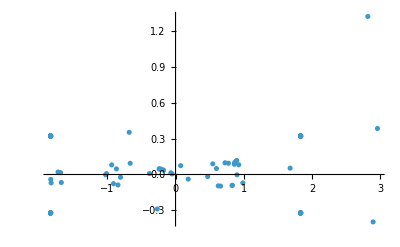

```mathematica
ListPlot[
{px,py}/.thing
,PlotRange->All
]
```

```mathematica
DeleteDuplicates[{1,7,8,4,3,4,1,9,9.00001,2},Abs[#1-#2]<0.001&]
```

{1,7,8,4,3,9,2}

```mathematica
Ret/.{Ret->1.9958737205135053,Imt->1.6495885824185181,px->1.8335583410657108,py->0.32168592089143405}
```

1.99587

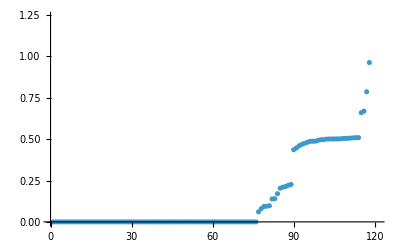

```mathematica
ListPlot[
Sort[
Abs[DsFunc[Ret+ⅈ*Imt,{px,py},r[[10]]]]/.thing
]
]
```

```mathematica
Re[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Re[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Im[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0,
Im[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]==0
```

### filter through fold point values, deleting duplicates, and setting tolerances for small values to be 0

```mathematica
ClearAll[foldpointsZeroed,foldpointsRounded,nonrepeatedfold,foldvalues,finalfolds]

Block[{px,py,k=5},

(*Define a function to set very small values to zero*)
setSmallValuesToZero[elem_,threshold_:10^-10]:=elem/. (x_Real/;Abs[x]<threshold)->0;

(*Apply the function to the array*)
foldpointsZeroed=setSmallValuesToZero[#,10^-10]&/@foldpoints;

(*Round the px and py values to the nearest tenth*)
roundPxPyValues[elem_]:=Module[{newElem=elem},newElem[[3,2]]=Round[newElem[[3,2]],0.2];
newElem[[4,2]]=Round[newElem[[4,2]],0.2];
newElem];

(*(*Apply the rounding function to the array*)
foldpointsRounded=roundPxPyValues/@foldpointsZeroed;*)

(*Define a custom comparison function*)sameTestQ[elem1_,elem2_]:=And[
Abs[(Ret/.elem1)-(Ret/.elem2)]<10^-1,
Abs[elem1[[2,2]]-elem2[[2,2]]]<10^-1,
Abs[elem1[[3,2]]-elem2[[3,2]]]<10^-1,
Abs[elem1[[4,2]]-elem2[[4,2]]]<10^-1
];

(*not actually rounded*)
foldpointsRounded=Select[foldpointsZeroed,Function[elem,
And[
(Abs[DsFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]/.elem)<10^-3,
(Abs[D2sFunc[Ret+ⅈ*Imt,{px,py},r[[k]]]]/.elem)<10^-3
]
]];

(*Apply DeleteDuplicates with the custom comparison function*)
nonrepeatedfold=DeleteDuplicates[foldpointsRounded,sameTestQ];
(*Make sure it's within one cyclic range (periodic), and for Imt bigger than 1.6 - as in the plot below you can see it needs high imagingary value*)
foldvalues=SortBy[Select[nonrepeatedfold,((Ret/. #)>=realMini&&(Ret/. #)<=realMaxi&&(Imt/. #)>0)&],(Ret/. #)&];

(*Print the results with a newline after each element*)
finalfolds=Column[foldvalues,ItemSize->{Automatic,1},Dividers->None];]

Print[finalfolds]
Print[Length[finalfolds[[1]]]]
```

{Ret→-2.21098,Imt→1.38039,px→-1.37566,py→-1.00101}
{Ret→-0.930616,Imt→1.38039,px→-1.37566,py→1.00101}
{Ret→0.930616,Imt→1.38039,px→1.37566,py→-1.00101}
{Ret→2.21098,Imt→1.38039,px→1.37566,py→1.00101}

4

make  sure  you  properly  filtered  through  the  fold  points, plot  them  onto  the  saddle  point  complex  plane, and  see  if  they  make  sense  or  not, for  the  given  variables, do  this  first!!

```mathematica
(*Extract the coordinates from finalfolds*)
foldcoordinates=foldvalues/. {Ret->x_,Imt->y_,px->z_,py->_}:>{x,y,z}
```

{{-2.21098,1.38039,-1.37566},{-0.930616,1.38039,-1.37566},{0.930616,1.38039,1.37566},{2.21098,1.38039,1.37566}}

### Saddle points plotted in complex plane, py fixed, and px varied with color

```mathematica
(*Preprocess the data to include colors based on the 3rd component*)
Block[
{py=0},

data1=Table[Select[validData[[i]],#[[4]]==py&],{i,Length[r]}];

points1=Table[{#[[1]],#[[2]]}&/@data1[[i]],{i,Length[r]}];

colors1=Table[ColorData["Rainbow"][Rescale[#[[3]],{-3,3(*minValue[[i]],maxValue[[i]]*)}]]&/@data1[[i]],{i,Length[r]}];

Manipulate[Graphics[{PointSize[Small],MapThread[{#2,Point[#1]}&,{points1[[i]],colors1[[i]]}],Black,PointSize[Medium],Point[foldcoordinates[[All,{1,2}]]]},Frame->True,FrameLabel->{"Real Time","Imaginary Time"},PlotLabel->"Saddle points in the Complex Plane, correctly indexed momenta",ImageSize->Large,PlotRange->{(*All*){realMin,realMax},{imagMin,imagMax}}],{i,Length[r]}]
]
```

### Find cusp points iterating through grid of seeds

```mathematica
cusppoints=Quiet[Block[{tguess, pxguess, pyguess,Retguess,Imtguess,ReKguess,ImKguess},
Retguess=-2;
Imtguess=1.2321;
pyguess=0;
pxguess=-3;
ReKguess=π/36;
ImKguess=0;
Table[Block[{Ret,Imt},
Retguess=Re[t];Imtguess=Im[t];
FindRoot[
{Re[DsFunc[Ret+ⅈ*Imt,{px,py},ReK+ⅈ*ImK]]==0,
Re[D2sFunc[Ret+ⅈ*Imt,{px,py},ReK+ⅈ*ImK]]==0,
Re[D3sFunc[Ret+ⅈ*Imt,{px,py},ReK+ⅈ*ImK]]==0,
Im[DsFunc[Ret+ⅈ*Imt,{px,py},ReK+ⅈ*ImK]]==0,
Im[D2sFunc[Ret+ⅈ*Imt,{px,py},ReK+ⅈ*ImK]]==0,
Im[D3sFunc[Ret+ⅈ*Imt,{px,py},ReK+ⅈ*ImK]]==0
},{Ret,Retguess},{Imt,Imtguess},{px, pxguess},{py,pyguess},{ReK,ReKguess},{ImK,ImKguess}]]
,{t,listofseeds1}]
]];
```

### filter through cusp point values, deleting duplicates, and setting tolerances for small values to be 0

```mathematica
ClearAll[cusppointsZeroed,cuspPointsrounded,nonrepeatedcusps,cuspvalues,filteredCusps,filteredCusps1,finalcusps]

Block[{px,py},
(*Define a function to set very small values to zero*)
setSmallValuesToZero[elem_,threshold_:10^-10]:=elem/. (x_Real/;Abs[x]<threshold)->0;

(*Apply the function to the array*)
cusppointsZeroed=setSmallValuesToZero[#,10^-10]&/@cusppoints;

(*Round the px and py values to the nearest tenth*)
roundPxPyValues[elem_]:=Module[{newElem=elem},newElem[[3,2]]=Round[newElem[[3,2]],0.2];
newElem[[4,2]]=Round[newElem[[4,2]],0.2];
newElem];

(*Apply the rounding function to the array*)
cuspPointsrounded=roundPxPyValues/@cusppointsZeroed;

(*Define a custom comparison function*)sameTestQ[elem1_,elem2_]:=Abs[elem1[[1,2]]-elem2[[1,2]]]<10^-1&&Abs[elem1[[2,2]]-elem2[[2,2]]]<10^-1&&Abs[elem1[[3,2]]-elem2[[3,2]]]<10^-1&&Abs[elem1[[4,2]]-elem2[[4,2]]]<10^-1;

(*Apply DeleteDuplicates with the custom comparison function*)
nonrepeatedcusps=DeleteDuplicates[cuspPointsrounded,sameTestQ];

(*Make sure it's within one cyclic range (periodic), and for Imt bigger than 0- as in the plot below you can see it needs to have imagingary value*)
cuspvalues=SortBy[Select[nonrepeatedcusps,((Ret/. #)>=realMini&&(Ret/. #)<=realMaxi&&(Imt/. #)>0)&],(Ret/. #)&];

(*Filter the results to only include elements where ImK is equal to 0*)
filteredCusps=Select[cuspvalues,(ImK/. #[[6]])==0&];
(*(*Further filter the results to only include elements where ReK is between 0 and 2π*)filteredCusps1=Select[filteredCusps,π/36<=(ReK/. #[[5]])<= 72π/36&];*)

(*Print the results with a newline after each element*)
finalcusps=Column[filteredCusps,ItemSize->{Automatic,1},Dividers->None];]


Print[finalcusps];
Print[Length[finalcusps[[1]]]]
```

{Ret→-1.5708,Imt→2.16118,px→-3.,py→0.,ReK→0.0929537,ImK→0}
{Ret→1.5708,Imt→2.16118,px→-3.,py→0.,ReK→3.04864,ImK→0}
{Ret→1.5708,Imt→2.16118,px→3.,py→0.,ReK→-0.0929537,ImK→0}

3

(*and then after figuring out how the fold points look int the saddle point plots, then TRY USE THESE ReK for saddle points value and a bit below and a bit above for the saddle plots, make sure that ReK is from 0 to 90 degrees*)

```mathematica
(*Extract the coordinates from finalfolds*)
cuspcoordinates=filteredCusps/. {Ret->x_,Imt->y_,px->z_,py->_,ReK->_,ImK->_}:>{x,y,z}
```

{{-1.5708,2.16118,-3.},{1.5708,2.16118,-3.},{1.5708,2.16118,3.}}

```mathematica
foldcoordinates
```

{{-2.21098,1.38039,-1.37566},{-0.930616,1.38039,-1.37566},{0.930616,1.38039,1.37566},{2.21098,1.38039,1.37566}}

```mathematica
(*Preprocess the data to include colors based on the 3rd component*)
Block[{py=0},data1=Table[Select[validData[[i]],#[[4]]==py&],{i,Length[r]}];
points1=Table[{#[[1]],#[[2]]}&/@data1[[i]],{i,Length[r]}];
colors1=Table[ColorData["Rainbow"][Rescale[#[[3]],{-3,3(*minValue[[i]],maxValue[[i]]*)}]]&/@data1[[i]],{i,Length[r]}];
Manipulate[Graphics[{PointSize[Small],MapThread[{#2,Point[#1]}&,{points1[[i]],colors1[[i]]}],Black,PointSize[Medium],Point[cuspcoordinates[[All,{1,2}]]]},Frame->True,FrameLabel->{"Real Time","Imaginary Time"},PlotLabel->"Saddle points in the Complex Plane, correctly indexed momenta",ImageSize->Large,PlotRange->{(*All*){realMin,realMax},{imagMin,imagMax}}],{i,Length[r]}]
]
```

### Saddle points plotted in complex plane, with px varied with color

```mathematica
Print[r[[10]]," and ",r[[14]]]
```

π/16 and π/36

```mathematica
validData[[5]]
```

```mathematica
finalfolds[[1,4]]
```

{Ret→2.21098,Imt→1.38039,px→1.37566,py→1.00101}

```mathematica
py/.finalfolds[[1,4]]
```

1.00101

```mathematica
Select[
validData[[5]],
Function[dataRow,dataRow[[4]]<(py/.finalfolds[[1,4]])]
]
```

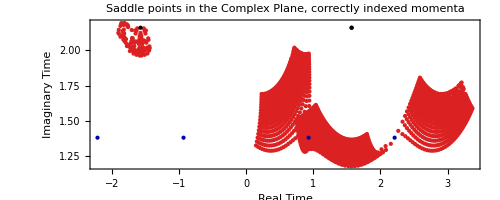

```mathematica
(*Preprocess the data to include colors based on the 3rd component*)
data2=Select[
validData[[5]],
Function[dataRow,And[
dataRow[[3]]>(px/.finalfolds[[1,4]]),
dataRow[[4]]<(py/.finalfolds[[1,4]])
]]
];
points2={#[[1]],#[[2]]}&/@data2; (*Only use the first two components for 2D plotting*)

(*Check the range of the 4th component*)
minValue=Min[data2[[All,4]]];
maxValue=Max[data2[[All,4]]];

colors2=ColorData["Rainbow"][Rescale[#[[3]],{minValue,maxValue}]]&/@data2;

(*Extract the coordinates from cuspcoordinates and foldcoordinates*)
cuspPoints=cuspcoordinates[[All,{1,2}]];
foldPoints=foldcoordinates[[All,{1,2}]];

Graphics[{PointSize[Small],MapThread[{#2,Point[#1]}&,{points2,colors2}],Black,PointSize[Large],Point[cuspPoints],Darker[Blue],PointSize[Large],Point[foldPoints]},Frame->True,FrameLabel->{"Real Time","Imaginary Time"},PlotLabel->"Saddle points in the Complex Plane, correctly indexed momenta",ImageSize->Full,PlotRange->All]
```

need to do: plot 2d complex plane, saddle points, vary px and py with slider, no color.

# ‘4D’ Plot Saddle points plot correctly plotted with px and py

```mathematica
(*Preprocess the data to include colors based on the 4th component*)data=Table[validData[[i]],{i,Length[r]}];
points=Table[{#[[1]],#[[2]],#[[3]]}&/@data[[i]],{i,Length[r]}];
colors=Table[ColorData["Rainbow"][Rescale[#[[4]],{-3,3}]]&/@data[[i]],{i,Length[r]}];

(*Extract the coordinates from cuspcoordinates and foldcoordinates*)
cuspPoints=cuspcoordinates[[All,{1,2,3}]];
foldPoints=foldcoordinates[[All,{1,2,3}]];
```

```mathematica
Manipulate[
Graphics3D[{
PointSize[Small],MapThread[{#2,Point[#1]}&,{points[[i]],colors[[i]]}],Black,PointSize[Medium],Point[cuspPoints],Black,PointSize[Medium],Point[foldPoints]
}
,Axes->True
,AxesLabel->{"Real Time","Imaginary Time","px"}
,PlotLabel->"4D Data Representation"
,ImageSize->950
,PlotRange->{{realMin,realMax},{imagMin,imagMax},{-3,3}}
,SphericalRegion->True,ViewPoint->{0,0,10},ViewVertical->{0,0,1}
,BoxRatios->{1,1,0.35}
]
,{i,Range[1,Length[r]],ControlType->Setter}]
```

```mathematica
foldPoints=foldcoordinates[[All,{1,2,3,4}]]
```

Part::partw: Part {1,2,3,4} of {-1.99587,1.64959,-1.8} does not exist.

{{-1.99587,1.64959,-1.8},{-1.14572,1.64959,-1.8},{1.14572,1.64959,1.8},{1.99587,1.64959,1.8}}⟦All,{1,2,3,4}⟧

```mathematica
foldcoordinates
```

{{-1.99587,1.64959,-1.8},{-1.14572,1.64959,-1.8},{1.14572,1.64959,1.8},{1.99587,1.64959,1.8}}

```mathematica
finalfolds
```

{Ret→-1.99587,Imt→1.64959,px→-1.8,py→-0.4}
{Ret→-1.14572,Imt→1.64959,px→-1.8,py→0.4}
{Ret→1.14572,Imt→1.64959,px→1.8,py→-0.4}
{Ret→1.99587,Imt→1.64959,px→1.8,py→0.4}

```mathematica
1.8
```